```mathematica
C1 = {{1,0},{0,0}};
R = {{Cos[Pi/3],-Sin[Pi/3]},{Sin[Pi/3],Cos[Pi/3]}};
C2 =R.C1.Transpose[R];
C3 =R.C2.Transpose[R];
C4 =R.C3.Transpose[R];
C5 =R.C4.Transpose[R];
C6 =R.C5.Transpose[R];
c1 = {1,0};
c2 = R.c1;
c3 = R.c2;
c4 = R.c3;
c5 = R.c4;
c6 = R.c5;
M[kx_,ky_] = C1 Sin[{kx,ky}.c1/2]^2+C2 Sin[{kx,ky}.c2/2]^2+C3 Sin[{kx,ky}.c3/2]^2+C4 Sin[{kx,ky}.c4/2]^2+C5 Sin[{kx,ky}.c5/2]^2+C6 Sin[{kx,ky}.c6/2]^2;
```

```mathematica
M[0,ky]//MatrixForm
Eigenvalues[M[0,ky]]
Series[Eigenvectors[M[k,k]],{k,0,3}]
```

(Sin[(√3 ky)/4]^2 | 0
0 | 3 Sin[(√3 ky)/4]^2)

{3 Sin[(√3 ky)/4]^2,Sin[(√3 ky)/4]^2}

{{-1+k^2/24+O[k]^4,1},{1+k^2/24+O[k]^4,1}}

```mathematica
Mat = {{a,b,c},{b,d,e},{c,e,f}};
MatrixPower[Mat,-1]
```

{{(-e^2+d f)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f),(c e-b f)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f),(-c d+b e)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f)},{(c e-b f)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f),(-c^2+a f)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f),(b c-a e)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f)},{(-c d+b e)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f),(b c-a e)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f),(-b^2+a d)/(-c^2 d+2 b c e-a e^2-b^2 f+a d f)}}

```mathematica
Mat2 = {{a,b},{c,d}};
Kmat = MatrixPower[Mat2,-1];
FullSimplify[D[Kmat,a]^2]//MatrixForm
FullSimplify[D[Kmat,b]^2] //MatrixForm
FullSimplify[D[Kmat,c]^2] //MatrixForm
FullSimplify[D[Kmat,d]^2]//MatrixForm
```

(d^4/(b c-a d)^4 | (b^2 d^2)/(b c-a d)^4
(c^2 d^2)/(b c-a d)^4 | (b^2 c^2)/(b c-a d)^4)

((c^2 d^2)/(b c-a d)^4 | (a^2 d^2)/(b c-a d)^4
c^4/(b c-a d)^4 | (a^2 c^2)/(b c-a d)^4)

((b^2 d^2)/(b c-a d)^4 | b^4/(b c-a d)^4
(a^2 d^2)/(b c-a d)^4 | (a^2 b^2)/(b c-a d)^4)

((b^2 c^2)/(b c-a d)^4 | (a^2 b^2)/(b c-a d)^4
(a^2 c^2)/(b c-a d)^4 | a^4/(b c-a d)^4)

```mathematica
ArcTan[I x]
```

ⅈ ArcTanh[x]

```mathematica
ArcSin[I x]
```

ⅈ ArcSinh[x]

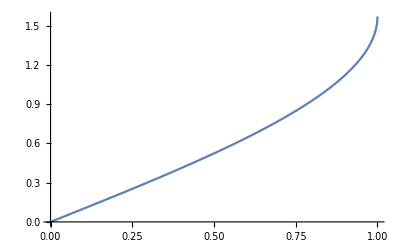

```mathematica
Plot[ArcSin[x],{x,0,1}]
```

```mathematica
mat = {{n-1,-1,-1,-1},{-1,n-1,-1,-1},{-1,-1,n-1,-1},{-1,-1,-1,n-1}}
mat2 = {{n-1,-1,-1,-1,-1,-1},{-1,n-1,-1,-1,-1,-1},{-1,-1,n-1,-1,-1,-1},{-1,-1,-1,n-1,-1,-1},{-1,-1,-1,-1,n-1,-1},{-1,-1,-1,-1,-1,n-1}}
```

{{-1+n,-1,-1,-1},{-1,-1+n,-1,-1},{-1,-1,-1+n,-1},{-1,-1,-1,-1+n}}

{{-1+n,-1,-1,-1,-1,-1},{-1,-1+n,-1,-1,-1,-1},{-1,-1,-1+n,-1,-1,-1},{-1,-1,-1,-1+n,-1,-1},{-1,-1,-1,-1,-1+n,-1},{-1,-1,-1,-1,-1,-1+n}}

```mathematica
MatrixForm[mat]
MatrixForm[mat2]
```

(-1+n | -1 | -1 | -1
-1 | -1+n | -1 | -1
-1 | -1 | -1+n | -1
-1 | -1 | -1 | -1+n)

(-1+n | -1 | -1 | -1 | -1 | -1
-1 | -1+n | -1 | -1 | -1 | -1
-1 | -1 | -1+n | -1 | -1 | -1
-1 | -1 | -1 | -1+n | -1 | -1
-1 | -1 | -1 | -1 | -1+n | -1
-1 | -1 | -1 | -1 | -1 | -1+n)

```mathematica
Inverse[mat]//MatrixForm
Inverse[mat2]//MatrixForm
```

((-3 n^2+n^3)/(-4 n^3+n^4) | n^2/(-4 n^3+n^4) | n^2/(-4 n^3+n^4) | n^2/(-4 n^3+n^4)
n^2/(-4 n^3+n^4) | (-3 n^2+n^3)/(-4 n^3+n^4) | n^2/(-4 n^3+n^4) | n^2/(-4 n^3+n^4)
n^2/(-4 n^3+n^4) | n^2/(-4 n^3+n^4) | (-3 n^2+n^3)/(-4 n^3+n^4) | n^2/(-4 n^3+n^4)
n^2/(-4 n^3+n^4) | n^2/(-4 n^3+n^4) | n^2/(-4 n^3+n^4) | (-3 n^2+n^3)/(-4 n^3+n^4))

((-5 n^4+n^5)/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6)
n^4/(-6 n^5+n^6) | (-5 n^4+n^5)/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6)
n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | (-5 n^4+n^5)/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6)
n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | (-5 n^4+n^5)/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6)
n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | (-5 n^4+n^5)/(-6 n^5+n^6) | n^4/(-6 n^5+n^6)
n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | n^4/(-6 n^5+n^6) | (-5 n^4+n^5)/(-6 n^5+n^6))

```mathematica
({{(-5 n^4+n^5)/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6)}, {n^4/(-6 n^5+n^6), (-5 n^4+n^5)/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6)}, {n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), (-5 n^4+n^5)/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6)}, {n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), (-5 n^4+n^5)/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6)}, {n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), (-5 n^4+n^5)/(-6 n^5+n^6), n^4/(-6 n^5+n^6)}, {n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), n^4/(-6 n^5+n^6), (-5 n^4+n^5)/(-6 n^5+n^6)}})
```

(n→6)[{{(-5 n^4+n^5)/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6)},{n^4/(-6 n^5+n^6),(-5 n^4+n^5)/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6)},{n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),(-5 n^4+n^5)/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6)},{n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),(-5 n^4+n^5)/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6)},{n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),(-5 n^4+n^5)/(-6 n^5+n^6),n^4/(-6 n^5+n^6)},{n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),n^4/(-6 n^5+n^6),(-5 n^4+n^5)/(-6 n^5+n^6)}}]

```mathematica
Eigenvectors[mat]
```

{{1,1,1,1},{-1,0,0,1},{-1,0,1,0},{-1,1,0,0}}

```mathematica
mat3 = {{1-(1-e)/3,-(1-e)/3,-(1-e)/3},{-(1-e)/3,1-(1-e)/3,-(1-e)/3},{-(1-e)/3,-(1-e)/3,1-(1-e)/3}}
```

{{1+1/3 (-1+e),1/3 (-1+e),1/3 (-1+e)},{1/3 (-1+e),1+1/3 (-1+e),1/3 (-1+e)},{1/3 (-1+e),1/3 (-1+e),1+1/3 (-1+e)}}

```mathematica
U = Eigenvectors[mat3]
```

{{-1,0,1},{-1,1,0},{1,1,1}}

```mathematica
Eigenvalues[mat3]
```

{1,1,e}

```mathematica
U. mat3 . Inverse[U]
```

(1+1/3 ((1-e)/3+1/3 (-1+e))+(1-e)/3+1/3 (-1+e) | 1/3 (-1+(1-e)/3+1/3 (-1+e))+2/3 ((1-e)/3+1/3 (-1+e))+1/3 (1+(1-e)/3+1/3 (-1+e)) | 1/3 (-1+(1-e)/3+1/3 (-1+e))+1/3 ((1-e)/3+1/3 (-1+e))+1/3 (1+(1-e)/3+1/3 (-1+e))
1/3 (-1+(1-e)/3+1/3 (-1+e))+2/3 ((1-e)/3+1/3 (-1+e))+1/3 (1+(1-e)/3+1/3 (-1+e)) | 1+1/3 ((1-e)/3+1/3 (-1+e))+(1-e)/3+1/3 (-1+e) | 1/3 (-1+(1-e)/3+1/3 (-1+e))+1/3 ((1-e)/3+1/3 (-1+e))+1/3 (1+(1-e)/3+1/3 (-1+e))
0 | 0 | e)

```mathematica
M2 = mat2/6/.n->6
```

{{5/6,-1/6,-1/6,-1/6,-1/6,-1/6},{-1/6,5/6,-1/6,-1/6,-1/6,-1/6},{-1/6,-1/6,5/6,-1/6,-1/6,-1/6},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6},{-1/6,-1/6,-1/6,-1/6,5/6,-1/6},{-1/6,-1/6,-1/6,-1/6,-1/6,5/6}}

```mathematica
M2
```

{{5/6,-1/6,-1/6,-1/6,-1/6,-1/6},{-1/6,5/6,-1/6,-1/6,-1/6,-1/6},{-1/6,-1/6,5/6,-1/6,-1/6,-1/6},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6},{-1/6,-1/6,-1/6,-1/6,5/6,-1/6},{-1/6,-1/6,-1/6,-1/6,-1/6,5/6}}

```mathematica
U = Eigenvectors[M2]
```

{{-1,0,0,0,0,1},{-1,0,0,0,1,0},{-1,0,0,1,0,0},{-1,0,1,0,0,0},{-1,1,0,0,0,0},{1,1,1,1,1,1}}

```mathematica
U.{th1,th2,th3,th4,th5,th6}//MatrixForm
```

(-th1+th6
-th1+th5
-th1+th4
-th1+th3
-th1+th2
th1+th2+th3+th4+th5+th6)

```mathematica
Simplify[{th1,th2,th3,th4,th5,th6}.Inverse[U]*6]//MatrixForm
```

(-th1-th2-th3-th4-th5+5 th6
-th1-th2-th3-th4+5 th5-th6
-th1-th2-th3+5 th4-th5-th6
-th1-th2+5 th3-th4-th5-th6
-th1+5 th2-th3-th4-th5-th6
th1+th2+th3+th4+th5+th6)

```mathematica
M2
```

{{5/6,-1/6,-1/6,-1/6,-1/6,-1/6},{-1/6,5/6,-1/6,-1/6,-1/6,-1/6},{-1/6,-1/6,5/6,-1/6,-1/6,-1/6},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6},{-1/6,-1/6,-1/6,-1/6,5/6,-1/6},{-1/6,-1/6,-1/6,-1/6,-1/6,5/6}}

```mathematica
Eigenvalues[M2]
P = DiagonalMatrix[{1,1,1,1,1,0}];
U = Eigenvectors[M2];
U.M2.Inverse[U];
UinvPU = Inverse[U].P.U
UinvPU.M2.UinvPU
```

{1,1,1,1,1,0}

{{5/6,-1/6,-1/6,-1/6,-1/6,-1/6},{-1/6,5/6,-1/6,-1/6,-1/6,-1/6},{-1/6,-1/6,5/6,-1/6,-1/6,-1/6},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6},{-1/6,-1/6,-1/6,-1/6,5/6,-1/6},{-1/6,-1/6,-1/6,-1/6,-1/6,5/6}}

{{5/6,-1/6,-1/6,-1/6,-1/6,-1/6},{-1/6,5/6,-1/6,-1/6,-1/6,-1/6},{-1/6,-1/6,5/6,-1/6,-1/6,-1/6},{-1/6,-1/6,-1/6,5/6,-1/6,-1/6},{-1/6,-1/6,-1/6,-1/6,5/6,-1/6},{-1/6,-1/6,-1/6,-1/6,-1/6,5/6}}

```mathematica
Inverse[mat3]
```

{{(1/3+(2 e)/3)/e,(1/3-e/3)/e,(1/3-e/3)/e},{(1/3-e/3)/e,(1/3+(2 e)/3)/e,(1/3-e/3)/e},{(1/3-e/3)/e,(1/3-e/3)/e,(1/3+(2 e)/3)/e}}

```mathematica
mat3
```

{{1+1/3 (-1+e),1/3 (-1+e),1/3 (-1+e)},{1/3 (-1+e),1+1/3 (-1+e),1/3 (-1+e)},{1/3 (-1+e),1/3 (-1+e),1+1/3 (-1+e)}}

```mathematica
Mat3 = mat3/.e->0
```

{{2/3,-1/3,-1/3},{-1/3,2/3,-1/3},{-1/3,-1/3,2/3}}

```mathematica
{th1,th2,th3}.Mat3.{th1,th2,th3}
```

th1 ((2 th1)/3-th2/3-th3/3)+th2 (-th1/3+(2 th2)/3-th3/3)+(-th1/3-th2/3+(2 th3)/3) th3

```mathematica
FullSimplify[%]
```

2/3 (th1^2+th2^2-th2 th3+th3^2-th1 (th2+th3))

```mathematica
Factor[%]
```

2/3 (th1^2-th1 th2+th2^2-th1 th3-th2 th3+th3^2)

```mathematica
Mat3
```

{{2/3,-1/3,-1/3},{-1/3,2/3,-1/3},{-1/3,-1/3,2/3}}

```mathematica
Mat3//MatrixForm
```

(2/3 | -1/3 | -1/3
-1/3 | 2/3 | -1/3
-1/3 | -1/3 | 2/3)

```mathematica
Mat2=(mat2/.n->6)/6;
{th1,th2,th3,th4,th5,th6}.Mat2.{th1,th2,th3,th4,th5,th6}
```

th1 ((5 th1)/6-th2/6-th3/6-th4/6-th5/6-th6/6)+th2 (-th1/6+(5 th2)/6-th3/6-th4/6-th5/6-th6/6)+th3 (-th1/6-th2/6+(5 th3)/6-th4/6-th5/6-th6/6)+th4 (-th1/6-th2/6-th3/6+(5 th4)/6-th5/6-th6/6)+th5 (-th1/6-th2/6-th3/6-th4/6+(5 th5)/6-th6/6)+(-th1/6-th2/6-th3/6-th4/6-th5/6+(5 th6)/6) th6

```mathematica
FullSimplify[%]
```

1/6 (5 th1^2+5 th2^2+5 th3^2-2 th3 th4+5 th4^2-2 th3 th5-2 th4 th5+5 th5^2-2 (th3+th4+th5) th6+5 th6^2-2 th2 (th3+th4+th5+th6)-2 th1 (th2+th3+th4+th5+th6))